Quantum Dot Systems

Single Quantum Dotpaclet:QuantumMob/QuantumPlaybook/tutorial/QuantumDotSystems#937496619 | Double Quantum Dotpaclet:QuantumMob/QuantumPlaybook/tutorial/QuantumDotSystems#517046295

Here, we consider a system of quantum dots that are described by the Hubbard model.

Qpaclet:QuantumMob/QuantumPlaybook/ref/QQuantumMob Package Symbol | Particle number operator
Hoppaclet:QuantumMob/QuantumPlaybook/ref/HopQuantumMob Package Symbol | Hopping operator
FermionBasispaclet:QuantumMob/QuantumPlaybook/ref/FermionBasisQuantumMob Package Symbol | Fermion basis with certain features

Some useful functions when studying quantum dot systems.

First, make sure the package is loaded.

```mathematica
Needs["QuantumMob`Q3`"]
```

Choose a symbol to denote the dot operators.

```mathematica
Let[Fermion,d]
```

It is also convenient to explicitly set the energy parameters to be real.

```mathematica
Let[Real,ϵ,t,U]
```

Single Quantum Dot

### Single-particle (quadratic or non-interacting) part

Let us start from the single-particle (quadratic) part of the Hamiltonian. There are several equivalent ways:

The most obvious method is using the fermion operators:

```mathematica
Dagger[d[Up]]**d[Up]
```

d_↑^†d_↑

The above has a short cut Q[...] as following:

```mathematica
Q[d[Up]]
```

d_↑^†d_↑

You need to sum over all spin (up and down):

```mathematica
Sum[Q[d[s]],{s,{Up,Down}}]
```

d_↓^†d_↓+d_↑^†d_↑

The above can be even simpler as the following two (equivalent) examples:

```mathematica
Q[d[{Up,Down}]]
Q[d[All]]
```

d_↓^†d_↓+d_↑^†d_↑

d_↓^†d_↓+d_↑^†d_↑

So, the non-interacting part of the QD Hamiltonian is given by

```mathematica
H0=ϵ*Q[d[All]]
```

ϵ (d_↓^†d_↓+d_↑^†d_↑)

### On-site interaction

Now, let us turn to the interaction (quartic) part:

```mathematica
Hint=U Q[d[Up]]**Q[d[Down]]
```

U d_↓^†d_↑^†d_↑d_↓

### Many-body eigenstates

Finally, the Hamiltonian for the quantum dot is given by

```mathematica
HH=H0+Hint
```

ϵ (d_↓^†d_↓+d_↑^†d_↑)+U d_↓^†d_↑^†d_↑d_↓

The above Hamiltonian may be described in graph as follows. Here, the vertex U with dashed lines denotes the interaction.

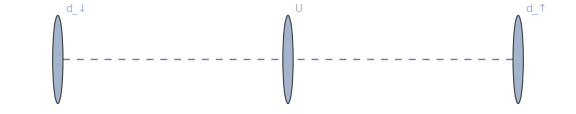

```mathematica
GraphForm[HH]
```

We need to construct a basis for the fermionic Fock space. Recall that the Hamiltonian conserves both the charge (Q) and spin (S). Therefore, it is a good idea to organize the basis accordingly. Here, note that the sector {Q=1,S=1/2} has only one state 1_(d_↑) but not 1_(d_↓). This is to avoid redundancy because both gives the same matrix elements.

```mathematica
bs=FermionBasis[d]
```

<|{0,0}→{␣},{1,1/2}→{1_(d_↑)},{2,0}→{-1_(d_↓)1_(d_↑)}|>

Naturally, the Hamiltonian is block diagonal in this basis.

```mathematica
big=MatrixIn[HH,bs,bs];
big=Values@KeyGroupBy[big,First,Values];
MatrixForm@Map[MatrixForm,big,{2}]
```

((0) | (0) | (0)
(0) | (ϵ) | (0)
(0) | (0) | (U+2 ϵ))

It is thus efficient to work on each diagonal block separately.

```mathematica
mat=MatrixIn[HH,bs];
MatrixForm/@mat
```

<|{0,0}→(0),{1,1/2}→(ϵ),{2,0}→(U+2 ϵ)|>

Double Quantum Dot

Let us now consider a double quantum dot (DQD). From the above example of single-orbital quantum dot, you now see that the following two statements are equivalent:

```mathematica
Dagger[d[1,Up]]**d[1,Up]
Q[d[1,Up]]
```

d_(1,↑)^†d_(1,↑)

d_(1,↑)^†d_(1,↑)

You should also be familiar with the following equivalent statements:

```mathematica
Sum[Q[d[j,Up]],{j,1,2}]
Q[d[{1,2},Up]]
```

d_(1,↑)^†d_(1,↑)+d_(2,↑)^†d_(2,↑)

d_(1,↑)^†d_(1,↑)+d_(2,↑)^†d_(2,↑)

What about the  sum over spin? The following two statements are equivalent:

```mathematica
Q[d[1,{Up,Down}]]
Q[d[1,All]]
```

d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)

d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)

The single-particle part of the two isolated quantum dots is given by

```mathematica
H0=ϵ*Q[d[{1,2},All]]
```

ϵ (d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)+d_(2,↓)^†d_(2,↓)+d_(2,↑)^†d_(2,↑))

Now, let us turn to the hopping between the two quantum dots.  Again one straightforward method is as following:

```mathematica
Sum[d[1,s]^Dagger**d[2,s],{s,{Up,Down}}]
```

d_(1,↓)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)

The above has a short-cut as following:

```mathematica
Hop[d[1,All],d[2,All]]
Hop[{d[1,All],d[2,All]}]
```

d_(1,↓)^†d_(2,↓)+d_(1,↓)^†d_(2,↑)+d_(1,↑)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)

d_(1,↓)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)

Do not forget to make it Hermitian. (There is one important reason why Hop[...] or FockHopping[...] does not include the hopping terms for both directions.)

```mathematica
PlusDagger@Hop[{d[1,All],d[2,All]}]
```

d_(1,↓)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)+d_(2,↓)^†d_(1,↓)+d_(2,↑)^†d_(1,↑)

So, the hopping part is given by

```mathematica
Ht=-PlusDagger@FockHopping[{d[1,All],d[2,All]}]
```

-d_(1,↓)^†d_(2,↓)-d_(1,↑)^†d_(2,↑)-d_(2,↓)^†d_(1,↓)-d_(2,↑)^†d_(1,↑)

Then, the overall single-particle part is given by

```mathematica
H1=H0+Ht
```

-d_(1,↓)^†d_(2,↓)-d_(1,↑)^†d_(2,↑)-d_(2,↓)^†d_(1,↓)-d_(2,↑)^†d_(1,↑)+ϵ (d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)+d_(2,↓)^†d_(2,↓)+d_(2,↑)^†d_(2,↑))

### On-site interactions

Here is the onsite interaction terms.

```mathematica
Hint=U(Q[d[1,Up]]**Q[d[1,Down]]+Q[d[2,Up]]**Q[d[2,Down]])
```

U (d_(1,↓)^†d_(1,↑)^†d_(1,↑)d_(1,↓)+d_(2,↓)^†d_(2,↑)^†d_(2,↑)d_(2,↓))

### Many-body eigenstates

Finally, the total Hamiltonian for the DQD is given by

```mathematica
HH=H1+Hint
```

-d_(1,↓)^†d_(2,↓)-d_(1,↑)^†d_(2,↑)-d_(2,↓)^†d_(1,↓)-d_(2,↑)^†d_(1,↑)+ϵ (d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)+d_(2,↓)^†d_(2,↓)+d_(2,↑)^†d_(2,↑))+U (d_(1,↓)^†d_(1,↑)^†d_(1,↑)d_(1,↓)+d_(2,↓)^†d_(2,↑)^†d_(2,↑)d_(2,↓))

The above Hamiltonian may be described in graph as follows. Here, the vertex U with dashed lines denotes the interaction and solid line indicates hopping.

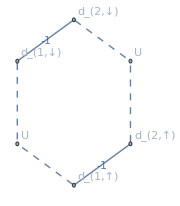

```mathematica
GraphForm[HH,ImageSize->Small]
```

Again, recall that the Hamiltonian conserves both the charge (Q) and spin (S). Therefore, it is a good idea to organize the basis accordingly. Here, note that in the sector {Q=1,S=1/2}, states 1_(d_(1,↓)) and 1_(d_(2,↓)) are missing. This is to avoid redundancy because both gives the same matrix elements.

```mathematica
bs=FermionBasis[d@{1,2}]
```

<|{0,0}→{␣},{1,1/2}→{1_(d_(2,↑)),1_(d_(1,↑))},{2,0}→{-1_(d_(1,↓))1_(d_(1,↑)),-(1_(d_(1,↓))1_(d_(2,↑)))/(√2)+(1_(d_(1,↑))1_(d_(2,↓)))/(√2),-1_(d_(2,↓))1_(d_(2,↑))},{2,1}→{1_(d_(1,↑))1_(d_(2,↑))},{3,1/2}→{-1_(d_(1,↓))1_(d_(1,↑))1_(d_(2,↑)),1_(d_(1,↑))1_(d_(2,↓))1_(d_(2,↑))},{4,0}→{1_(d_(1,↓))1_(d_(1,↑))1_(d_(2,↓))1_(d_(2,↑))}|>

Naturally, the Hamiltonian is block diagonal in this basis.

```mathematica
big=MatrixIn[HH,bs,bs];
big=KeyGroupBy[big,First,Values];
MatrixForm@Values@Map[MatrixForm,big,{2}]
```

((0) | (0 | 0) | (0 | 0 | 0) | (0) | (0 | 0) | (0)
(0
0) | (ϵ | -1
-1 | ϵ) | (0 | 0 | 0
0 | 0 | 0) | (0
0) | (0 | 0
0 | 0) | (0
0)
(0
0
0) | (0 | 0
0 | 0
0 | 0) | (U+2 ϵ | -√2 | 0
-√2 | 2 ϵ | -√2
0 | -√2 | U+2 ϵ) | (0
0
0) | (0 | 0
0 | 0
0 | 0) | (0
0
0)
(0) | (0 | 0) | (0 | 0 | 0) | (2 ϵ) | (0 | 0) | (0)
(0
0) | (0 | 0
0 | 0) | (0 | 0 | 0
0 | 0 | 0) | (0
0) | (U+3 ϵ | -1
-1 | U+3 ϵ) | (0
0)
(0) | (0 | 0) | (0 | 0 | 0) | (0) | (0 | 0) | (2 (U+2 ϵ)))

Therefore, it is efficient to consider each block separately.

```mathematica
mat=MatrixIn[HH,bs];
MatrixForm/@mat
```

<|{0,0}→(0),{1,1/2}→(ϵ | -1
-1 | ϵ),{2,0}→(U+2 ϵ | -√2 | 0
-√2 | 2 ϵ | -√2
0 | -√2 | U+2 ϵ),{2,1}→(2 ϵ),{3,1/2}→(U+3 ϵ | -1
-1 | U+3 ϵ),{4,0}→(2 (U+2 ϵ))|>

| Related Guides
▪Quantum Information Systems
▪Quantum Many-Body Systems
▪Quantum Spin Systems

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Information Systems with Q3
▪Quantum Many-Body Systems with Q3
▪Quantum Spin Systems with Q3